```mathematica
sx=100;
sy= 100;
sz=50;
SetDirectory["F:\\Mphil Project\\simulation\\6+1\\new2"];
```

```mathematica
powC=0;
powS =1;
Pol = 90;
Pha = 0;
Ang = 90;
powSC=0;
wl=4;
```

```mathematica
t1 = Import["F:\\Mphil Project\\simulation\\6+1 beams un-pure\\out.data", "Table"];
t2 = Table[t1[[(sy +1)*(i-1)  + j]][[k]], {i, 1, sz}, {j, 1, sy}, {k, 1, sx}];
M = Max[t2]
M 4
```

5.98775

23.951

```mathematica
since 4 second will show nothing, set cut off M 4
```

```mathematica
sc=Table[x,{x,5,10,0.5}];
1/sc;
a1=M 4/sc;
```

```mathematica
Do[
a=a1[[i]]; 
b= a+0.5;
g1=ListContourPlot3D[t2, Mesh -> False, Contours->{a,b},BoxRatios->Automatic,MaxPlotPoints->40,ContourStyle->{Green,Yellow},ViewPoint->{0,0,Infinity}];
g2=ListContourPlot3D[t2, Mesh -> False, Contours->{a, b},BoxRatios->Automatic,MaxPlotPoints->40,ContourStyle->{Green,Yellow},ViewPoint->{0,Infinity,0}];
g3=ListContourPlot3D[t2, Mesh -> False, Contours->{a, b},BoxRatios->Automatic,MaxPlotPoints->40,ContourStyle->{Green,Yellow},ViewPoint->{5,5,10},PlotLabel->"Central Beam Power (L-Cir) : "<>ToString[powC]<>" ; Side Beam Power "<>ToString[powS]<>"\n Polarization : "<>ToString[Pol]<>" ; Phase : "<>ToString[Pha]<>" ; Angle : "<>ToString[Ang]<>" ; Circular side : "<>ToString[powSC]<>" \n Cross Section : "<>ToString[wl]<>"x"<>ToString[wl]<>" wavelength ; Max intensity : "<>ToString[M]<>" ; Cut-off Dosage: "<>ToString[(M 4)]<>"\n Exposure Time (s): "<>ToString[sc[[i]]]<>"; Inner[Yellow] (absoulte): "<>ToString[b]<>" ; Outer[Green] (absolue): "<>ToString[a]<>" \n "];
Export["Deg "<>ToString[Ang]<>" - Pha "<>ToString[Pha]<>" - CP "<>ToString[powC]<>" - Pol "<>ToString[Pol]<> " - "<>ToString[sc[[i]] ]<>"s.jpg" ,Show[GraphicsGrid[{{g1,g3},{g2,SpanFromAbove}}],ImageSize->1000]];
,{i,1,Length[a1]}]
```

```mathematica
********************************************************************************************
```

```mathematica
a1=Table[x,{x,0.1,0.9,0.05}];
```

```mathematica
Do[
a=a1[[i]]; 
b= a+0.05;
g1=ListContourPlot3D[t2, Mesh -> False, Contours->{M a,M b},BoxRatios->Automatic,MaxPlotPoints->40,ContourStyle->{Green,Yellow},ViewPoint->{0,0,Infinity}];
g2=ListContourPlot3D[t2, Mesh -> False, Contours->{M a, M b},BoxRatios->Automatic,MaxPlotPoints->40,ContourStyle->{Green,Yellow},ViewPoint->{0,Infinity,0}];
g3=ListContourPlot3D[t2, Mesh -> False, Contours->{M a,M b},BoxRatios->Automatic,MaxPlotPoints->40,ContourStyle->{Green,Yellow},ViewPoint->{5,5,10},PlotLabel->"Central Beam Power (L-Cir) : "<>ToString[powC]<>" ; Side Beam Power "<>ToString[powS]<>"\n Polarization : "<>ToString[Pol]<>" ; Phase : "<>ToString[Pha]<>" ; Angle : "<>ToString[Ang]<>" ; Circular side : "<>ToString[powSC]<>" \n Cross Section : "<>ToString[wl]<>"x"<>ToString[wl]<>" wavelength ; Max intensity : "<>ToString[M]<>"\n Inner[Yellow] (relative): "<>ToString[b]<>" ; Outer[Green] (relative): "<>ToString[a]<>" \n "];
Export["Deg "<>ToString[Ang]<>" - Pha "<>ToString[Pha]<>" - CP "<>ToString[powC]<>" - Pol "<>ToString[Pol]<> " - "<>ToString[a ]<>"s.jpg" ,Show[GraphicsGrid[{{g1,g3},{g2,SpanFromAbove}}],ImageSize->1000]];
,{i,1,Length[a1]}]
```

```mathematica
t1 = Import["F:\\Mphil Project\\simulation\\6+1 beams un-pure\\out_dirty.data", "Table"];
t2 = Table[t1[[(sy +1)*(i-1)  + j]][[k]], {i, 1, sz}, {j, 1, sy}, {k, 1, sx}];
```

```mathematica
a=0.18;
g1=ListContourPlot3D[t2, Mesh -> False, Contours->{M a,M b},BoxRatios->Automatic,MaxPlotPoints->40,ContourStyle->{Green,Yellow},ViewPoint->{0,0,Infinity}];
g2=ListContourPlot3D[t2, Mesh -> False, Contours->{M a, M b},BoxRatios->Automatic,MaxPlotPoints->40,ContourStyle->{Green,Yellow},ViewPoint->{0,Infinity,0}];
g3=ListContourPlot3D[t2, Mesh -> False, Contours->{M a,M b},BoxRatios->Automatic,MaxPlotPoints->40,ContourStyle->{Green,Yellow},ViewPoint->{5,5,10},PlotLabel->"Central Beam Power (L-Cir) : "<>ToString[powC]<>" ; Side Beam Power "<>ToString[powS]<>"\n Polarization : "<>ToString[Pol]<>" ; Phase : "<>ToString[Pha]<>" ; Angle : "<>ToString[Ang]<>" ; Circular side : "<>ToString[powSC]<>"\n Yellow : "<>ToString[b]<>" ; Green : "<>ToString[a]<>" ; Cross Section : "<>ToString[wl]<>"x"<>ToString[wl]<>" wavelength \n "];
Export["Deg "<>ToString[Ang]<>" - Pha "<>ToString[Pha]<>" - CP "<>ToString[powC]<>" ("<>ToString[b]<>","<>ToString[a]<>").jpg" ,Show[GraphicsGrid[{{g1,g3},{g2,SpanFromAbove}}],ImageSize->1000]];
```

```mathematica
t3 = Table[t1[[(sy +1)*(i-1)  + j]][[k]], {i, 1,25}, {j, 1, sy}, {k, 1, sx}];
```

```mathematica
ListContourPlot3D[t3, Mesh -> False, Contours->{M 0.2,M 0.8},BoxRatios->Automatic,MaxPlotPoints->40,ContourStyle->{{Green,Opacity[0.5]},Yellow},ViewPoint->{0,Infinity,0}]
```

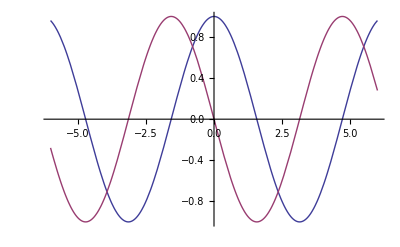

```mathematica
Plot[{Cos[x], Cos[x+π/2]},{x,-6,6}]
```